```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
Remove["Global`*"]
```

```mathematica
b:= 1/4
Subscript[a, 1]:=1
Subscript[a, 2]:=1
γ:=Pi/3 (* 60 deg *)
```

```mathematica
eqs:={a2-> b Cos[θ]-Subscript[a, 1],
b2-> b Sin[θ],
a3-> b(Cos[θ]Cos[γ]-Sin[θ]Sin[γ]),
b3-> b(Cos[θ]Sin[γ]+Sin[θ]Cos[γ])-Subscript[a, 2]}
```

```mathematica
weirs:={Cos[θ]->(1-t^2)/(1+t^2),Sec[θ]->(1+t^2)/(1-t^2),Sin[θ]->(2t)/(1+t^2),Csc[θ]->(1+t^2)/(2t),Tan[θ/2]->t}
```

```mathematica
p1:=x^2+y^2-> Subscript[l, 1]^2
p2:=(x+a2)^2+(y+b2)^2-Subscript[l, 2]^2==0
p3:=(x+a3)^2+(y+b3)^2-Subscript[l, 3]^2==0
```

```mathematica
Subscript[p2, exp]=Expand[p2]/.p1
Subscript[p3, exp]=Expand[p3]/.p1
```

a2^2+b2^2+2 a2 x+2 b2 y+l_1^2-l_2^2==0

a3^2+b3^2+2 a3 x+2 b3 y+l_1^2-l_3^2==0

```mathematica
Sols=Simplify[Solve[{Subscript[p2, exp], Subscript[p3, exp]},{x,y}]]
```

{{x→-(-2 b3 (a2^2+b2^2+l_1^2-l_2^2)+2 b2 (a3^2+b3^2+l_1^2-l_3^2))/(4 a3 b2-4 a2 b3),y→(a2^2 a3-a2 a3^2+a3 b2^2-a2 b3^2+(-a2+a3) l_1^2-a3 l_2^2+a2 l_3^2)/(-2 a3 b2+2 a2 b3)}}

```mathematica
x=Cancel[x/.Sols]
```

{(-a3^2 b2+a2^2 b3+b2^2 b3-b2 b3^2-b2 l_1^2+b3 l_1^2-b3 l_2^2+b2 l_3^2)/(2 (a3 b2-a2 b3))}

```mathematica
y=Cancel[y/.Sols]
```

{(-a2^2 a3+a2 a3^2-a3 b2^2+a2 b3^2+a2 l_1^2-a3 l_1^2+a3 l_2^2-a2 l_3^2)/(2 (a3 b2-a2 b3))}

```mathematica
n1:=Numerator[x]
n2:=Numerator[y]
d:=Denominator[x]
```

```mathematica
f=n1^2+n2^2-Subscript[l, 1]^2 d^2
```

{-4 (a3 b2-a2 b3)^2 l_1^2+(-a2^2 a3+a2 a3^2-a3 b2^2+a2 b3^2+a2 l_1^2-a3 l_1^2+a3 l_2^2-a2 l_3^2)^2+(-a3^2 b2+a2^2 b3+b2^2 b3-b2 b3^2-b2 l_1^2+b3 l_1^2-b3 l_2^2+b2 l_3^2)^2}

```mathematica
ff=f/.eqs/.weirs
```

{-4 ((t (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2))))/(8 (1+t^2))-(-1+(1-t^2)/(4 (1+t^2))) (-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2)))))^2 l_1^2+(-(t (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2)))^2)/(32 (1+t^2))+(t^2 (-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2)))))/(4 (1+t^2)^2)+(-1+(1-t^2)/(4 (1+t^2)))^2 (-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2))))-(t (-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2))))^2)/(2 (1+t^2))-(t l_1^2)/(2 (1+t^2))+(-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2)))) l_1^2-(-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2)))) l_2^2+(t l_3^2)/(2 (1+t^2)))^2+(-(t^2 (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2))))/(16 (1+t^2)^2)-1/4 (-1+(1-t^2)/(4 (1+t^2)))^2 (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2)))+1/16 (-1+(1-t^2)/(4 (1+t^2))) (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2)))^2+(-1+(1-t^2)/(4 (1+t^2))) (-1+1/4 (t/(1+t^2)+(√3 (1-t^2))/(2 (1+t^2))))^2+(-1+(1-t^2)/(4 (1+t^2))) l_1^2-1/4 (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2))) l_1^2+1/4 (-(√3 t)/(1+t^2)+(1-t^2)/(2 (1+t^2))) l_2^2-(-1+(1-t^2)/(4 (1+t^2))) l_3^2)^2}

```mathematica
ff2=Cancel[FullSimplify[ff]]
```

{1/(4096 (1+t^2)^3)(4869-1656 √3-1224 √3 t+22183 t^2-4312 √3 t^2-2304 t^3-4624 √3 t^3+30143 t^4+2744 √3 t^4-6400 t^5-3400 √3 t^5+16925 t^6+5400 √3 t^6+1392 l_1^2-192 √3 l_1^2+9344 t l_1^2-5120 √3 t l_1^2+5968 t^2 l_1^2-2752 √3 t^2 l_1^2+16640 t^3 l_1^2-8192 √3 t^3 l_1^2+1616 t^4 l_1^2-2880 √3 t^4 l_1^2+7296 t^5 l_1^2-3072 √3 t^5 l_1^2-2960 t^6 l_1^2-320 √3 t^6 l_1^2+7424 l_1^4-1024 √3 l_1^4+2048 t l_1^4-2048 √3 t l_1^4+24320 t^2 l_1^4-1024 √3 t^2 l_1^4+4096 t^3 l_1^4-4096 √3 t^3 l_1^4+26368 t^4 l_1^4+1024 √3 t^4 l_1^4+2048 t^5 l_1^4-2048 √3 t^5 l_1^4+9472 t^6 l_1^4+1024 √3 t^6 l_1^4-5712 l_2^2+1344 √3 l_2^2-3200 t l_2^2+3200 √3 t l_2^2-21616 t^2 l_2^2+1856 √3 t^2 l_2^2-256 t^3 l_2^2+4352 √3 t^3 l_2^2-28144 t^4 l_2^2-2368 √3 t^4 l_2^2+2944 t^5 l_2^2+1152 √3 t^5 l_2^2-12240 t^6 l_2^2-2880 √3 t^6 l_2^2-9472 l_1^2 l_2^2+2048 √3 l_1^2 l_2^2+2048 √3 t l_1^2 l_2^2-26368 t^2 l_1^2 l_2^2+2048 √3 t^2 l_1^2 l_2^2+4096 √3 t^3 l_1^2 l_2^2-24320 t^4 l_1^2 l_2^2-2048 √3 t^4 l_1^2 l_2^2+2048 √3 t^5 l_1^2 l_2^2-7424 t^6 l_1^2 l_2^2-2048 √3 t^6 l_1^2 l_2^2+4352 l_2^4-1024 √3 l_2^4-2048 t l_2^4+13056 t^2 l_2^4-1024 √3 t^2 l_2^4-4096 t^3 l_2^4+13056 t^4 l_2^4+1024 √3 t^4 l_2^4-2048 t^5 l_2^4+4352 t^6 l_2^4+1024 √3 t^6 l_2^4-5328 l_3^2+1152 √3 l_3^2+1152 √3 t l_3^2-24304 t^2 l_3^2+3200 √3 t^2 l_3^2+4352 √3 t^3 l_3^2-30576 t^4 l_3^2-1152 √3 t^4 l_3^2+3200 √3 t^5 l_3^2-11600 t^6 l_3^2-3200 √3 t^6 l_3^2-5376 l_1^2 l_3^2-4096 t l_1^2 l_3^2+2048 √3 t l_1^2 l_3^2-22272 t^2 l_1^2 l_3^2-8192 t^3 l_1^2 l_3^2+4096 √3 t^3 l_1^2 l_3^2-28416 t^4 l_1^2 l_3^2-4096 t^5 l_1^2 l_3^2+2048 √3 t^5 l_1^2 l_3^2-11520 t^6 l_1^2 l_3^2+768 l_2^2 l_3^2+4096 t l_2^2 l_3^2-2048 √3 t l_2^2 l_3^2+256 t^2 l_2^2 l_3^2+8192 t^3 l_2^2 l_3^2-4096 √3 t^3 l_2^2 l_3^2-1792 t^4 l_2^2 l_3^2+4096 t^5 l_2^2 l_3^2-2048 √3 t^5 l_2^2 l_3^2-1280 t^6 l_2^2 l_3^2+2304 l_3^4+11008 t^2 l_3^4+15104 t^4 l_3^4+6400 t^6 l_3^4)}

```mathematica
ff2=Numerator[ff2]//N
```

{2000.72-2120.03 t+14714.4 t^2-10313. t^3+34895.7 t^4-12289. t^5+26278.1 t^6+1059.45 l_1^2+475.9 t l_1^2+1201.4 t^2 l_1^2+2451.04 t^3 l_1^2-3372.31 t^4 l_1^2+1975.14 t^5 l_1^2-3514.26 t^6 l_1^2+5650.38 l_1^4-1499.24 t l_1^4+22546.4 t^2 l_1^4-2998.48 t^3 l_1^4+28141.6 t^4 l_1^4-1499.24 t^5 l_1^4+11245.6 t^6 l_1^4-3384.12 l_2^2+2342.56 t l_2^2-18401.3 t^2 l_2^2+7281.89 t^3 l_2^2-32245.5 t^4 l_2^2+4939.32 t^5 l_2^2-17228.3 t^6 l_2^2-5924.76 l_1^2 l_2^2+3547.24 t l_1^2 l_2^2-22820.8 t^2 l_1^2 l_2^2+7094.48 t^3 l_1^2 l_2^2-27867.2 t^4 l_1^2 l_2^2+3547.24 t^5 l_1^2 l_2^2-10971.2 t^6 l_1^2 l_2^2+2578.38 l_2^4-2048. t l_2^4+11282.4 t^2 l_2^4-4096. t^3 l_2^4+14829.6 t^4 l_2^4-2048. t^5 l_2^4+6125.62 t^6 l_2^4-3332.68 l_3^2+1995.32 t l_3^2-18761.4 t^2 l_3^2+7537.89 t^3 l_3^2-32571.3 t^4 l_3^2+5542.56 t^5 l_3^2-17142.6 t^6 l_3^2-5376. l_1^2 l_3^2-548.76 t l_1^2 l_3^2-22272. t^2 l_1^2 l_3^2-1097.52 t^3 l_1^2 l_3^2-28416. t^4 l_1^2 l_3^2-548.76 t^5 l_1^2 l_3^2-11520. t^6 l_1^2 l_3^2+768. l_2^2 l_3^2+548.76 t l_2^2 l_3^2+256. t^2 l_2^2 l_3^2+1097.52 t^3 l_2^2 l_3^2-1792. t^4 l_2^2 l_3^2+548.76 t^5 l_2^2 l_3^2-1280. t^6 l_2^2 l_3^2+2304. l_3^4+11008. t^2 l_3^4+15104. t^4 l_3^4+6400. t^6 l_3^4}

```mathematica
Subscript[ff2, coef]=CoefficientList[ff2,t]
```

{{2000.72+1059.45 l_1^2+5650.38 l_1^4-3384.12 l_2^2-5924.76 l_1^2 l_2^2+2578.38 l_2^4-3332.68 l_3^2-5376. l_1^2 l_3^2+768. l_2^2 l_3^2+2304. l_3^4,-2120.03+475.9 l_1^2-1499.24 l_1^4+2342.56 l_2^2+3547.24 l_1^2 l_2^2-2048. l_2^4+1995.32 l_3^2-548.76 l_1^2 l_3^2+548.76 l_2^2 l_3^2,14714.4+1201.4 l_1^2+22546.4 l_1^4-18401.3 l_2^2-22820.8 l_1^2 l_2^2+11282.4 l_2^4-18761.4 l_3^2-22272. l_1^2 l_3^2+256. l_2^2 l_3^2+11008. l_3^4,-10313.+2451.04 l_1^2-2998.48 l_1^4+7281.89 l_2^2+7094.48 l_1^2 l_2^2-4096. l_2^4+7537.89 l_3^2-1097.52 l_1^2 l_3^2+1097.52 l_2^2 l_3^2,34895.7-3372.31 l_1^2+28141.6 l_1^4-32245.5 l_2^2-27867.2 l_1^2 l_2^2+14829.6 l_2^4-32571.3 l_3^2-28416. l_1^2 l_3^2-1792. l_2^2 l_3^2+15104. l_3^4,-12289.+1975.14 l_1^2-1499.24 l_1^4+4939.32 l_2^2+3547.24 l_1^2 l_2^2-2048. l_2^4+5542.56 l_3^2-548.76 l_1^2 l_3^2+548.76 l_2^2 l_3^2,26278.1-3514.26 l_1^2+11245.6 l_1^4-17228.3 l_2^2-10971.2 l_1^2 l_2^2+6125.62 l_2^4-17142.6 l_3^2-11520. l_1^2 l_3^2-1280. l_2^2 l_3^2+6400. l_3^4}}

```mathematica
Subscript[ff2, coef]=Collect[Subscript[ff2, coef],{Subscript[l, 1],Subscript[l, 2],Subscript[l, 3]}]
```

{{2000.72+5650.38 l_1^4+2578.38 l_2^4-3332.68 l_3^2+2304. l_3^4+l_1^2 (1059.45-5924.76 l_2^2-5376. l_3^2)+l_2^2 (-3384.12+768. l_3^2),-2120.03-1499.24 l_1^4-2048. l_2^4+1995.32 l_3^2+l_1^2 (475.9+3547.24 l_2^2-548.76 l_3^2)+l_2^2 (2342.56+548.76 l_3^2),14714.4+22546.4 l_1^4+11282.4 l_2^4-18761.4 l_3^2+11008. l_3^4+l_1^2 (1201.4-22820.8 l_2^2-22272. l_3^2)+l_2^2 (-18401.3+256. l_3^2),-10313.-2998.48 l_1^4-4096. l_2^4+7537.89 l_3^2+l_1^2 (2451.04+7094.48 l_2^2-1097.52 l_3^2)+l_2^2 (7281.89+1097.52 l_3^2),34895.7+28141.6 l_1^4+14829.6 l_2^4-32571.3 l_3^2+15104. l_3^4+l_1^2 (-3372.31-27867.2 l_2^2-28416. l_3^2)+l_2^2 (-32245.5-1792. l_3^2),-12289.-1499.24 l_1^4-2048. l_2^4+5542.56 l_3^2+l_1^2 (1975.14+3547.24 l_2^2-548.76 l_3^2)+l_2^2 (4939.32+548.76 l_3^2),26278.1+11245.6 l_1^4+6125.62 l_2^4-17142.6 l_3^2+6400. l_3^4+l_1^2 (-3514.26-10971.2 l_2^2-11520. l_3^2)+l_2^2 (-17228.3-1280. l_3^2)}}

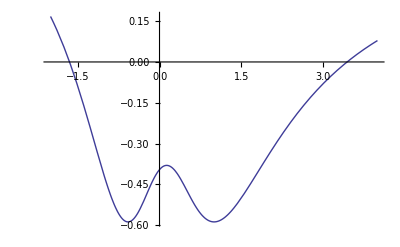

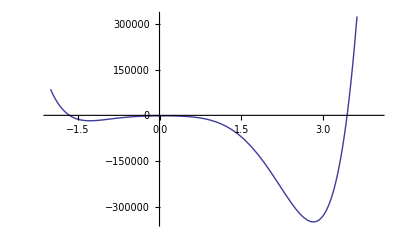

{{t→-1.6514},{t→3.44271}}

{-2.05261,2.57621}

{-1619.98+960.792 t-8300.87 t^2+740.315 t^3-8745.29 t^4-4316.48 t^5+2031.59 t^6}

```mathematica
input:={Subscript[l, 1]-> 0.8,Subscript[l, 2]-> 0.8,Subscript[l, 3]-> 0.8}
Plot[ff/.input,{t,-2,4}]
Plot[ff2/.input,{t,-2,4}]
ss1=Solve[ff2==0/.input,t,Reals]
ss2=2 ArcTan[t/.ss1]
ff2/.input
```

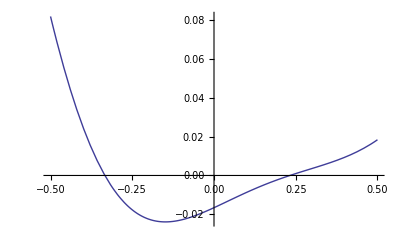

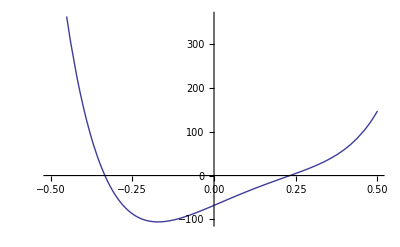

{{t→-0.333662},{t→0.232197}}

```mathematica
input:={Subscript[l, 1]-> 0.815,Subscript[l, 2]-> 0.847,Subscript[l, 3]-> 0.48}
Plot[ff/.input,{t,-0.5,0.5}]
Plot[ff2/.input,{t,-0.5,0.5}]
ss2=Solve[ff2==0/.input,t,Reals]
```

```mathematica
(*Solve[f==0,t, Reals]*)
```